# Wolfram语言中的图像处理技术 —— 案例分享 Image Processing in Wolfram Language —— a showcase

## Silvia, Wolfram Research

## 微信公众号：WolframChina -Graphics- -Graphics-微博公众号：WolframChina -Graphics-

## 内容提要 ABSTRACT

在该讲座中我们将向大家展示一些 Wolfram 语言带来的 “非常规” 的图像处理方法。我们准备了三个有趣的案例，每一个都将从不同侧面展示 Wolfram 语言 “一切皆可计算” 的核心精神。希望本演讲能给大家带来一个轻松愉快的体验。

In this presentation we bring 3 interesting and unconventional examples to showcase, when it comes to image processing, what it means when we say “everything is about computation”. We wish you enjoy the ride!

## 案例1：与外部渲染器协作制作磨砂/水纹玻璃效果 Case 1: A patterned-glass filter through external renderer

问题：我们手上有一张普通照片，想给它加上磨砂或水纹玻璃效果，请问可以如何做？

Question: How to add a frosted-glass effect to a photo?

-Graphics-

## 案例1 / Case 1

```mathematica
SetDirectory["case 1"];
```

```mathematica
img=Import@"orig-thumbnail.png";
```

-Graphics-

## 案例1 / Case 1

### 轻松模式：使用内置函数 ImageEffect Easy mode: Using the built-in function ImageEffect

```mathematica
ImageEffect[img,{"Jitter",5}]//Image
```

-Graphics-

优点：简便快捷

缺点：风格固定、可定制化程度不高

## 案例1 / Case 1

### 困难模式：使用 ImageFilter、ImageTransformation 等内置函数 Hard mode: Using the built-in function ImageFilter, ImageTransformation, etc.

可能的方法有很多。此处按下不表，留给大家自己探索。

Lots of interesting possibilities! An open question for audiences!

## 案例1 / Case 1

### 休闲模式：自制玻璃3D模型，调用外部渲染器实现效果 Insane mode: Build your own 3D model of the glass, feed it to an external renderer!

我们会涉及到三种尺寸：
图片的尺寸 imgSize, 3D模型的基本尺寸 glassScaleRange, 玻璃表面的纹理坐标 [0,1]×[0,1]

用 RescalingTransform 来实现不同尺寸之间的自由转换

## 案例1 / Case 1

### 休闲模式 / Insane mode

首先设定模型基本尺寸。
为了整个工具链的计算方便，我们将图像尺寸等比例缩放到10以内的范围：

```mathematica
imgSize=ImageDimensions@img;
```

```mathematica
glassScaleRange=imgSize/200//{-#,#}ᵀ&//N
```

{{-3.,3.},{-3.66,3.66}}

最简单的出发点：用 DiscretizeRegion 三角剖分一个长方形

```mathematica
baseMesh=glassScaleRangeᵀ//pipe[
Apply@Cuboid
,DiscretizeRegion[#,MaxCellMeasure->.01]&
];
baseVtxSet=MeshCoordinates[baseMesh];
```

```mathematica
baseVtxSet//pipe[
RescalingTransform[glassScaleRange,{{1,1},imgSize}ᵀ]
,{#,RGBColor@@@ImageValue[img,#]}&
,MapThread[{#2,AbsolutePointSize[4],Point@#1}&]
,Graphics[#,Frame->True]&
]
```

-Graphics-

## 案例1 / Case 1

### 休闲模式 / Insane mode

更有意思的剖分方式：MeshRefinementFunction

```mathematica
meshRefineMask=ImageSaliencyFilter[img,Method->"HistogramContrast"]//GaussianFilter[#,10]&//ImageAdjust//#^(1/2)&
```

-Graphics-

```mathematica
baseMesh=Block[{𝕧,𝓂}
,glassScaleRangeᵀ//pipe[
Apply[Cuboid]
,Inactive[DiscretizeRegion][#
,MaxCellMeasure->.01
,MeshRefinementFunction->Inactive[Function][{𝕧,𝓂}
,And[𝓂>.001
,𝕧//pipe[Mean
,RescalingTransform[glassScaleRange,{{1,1},imgSize}ᵀ]
,Inactive[ImageValue][meshRefineMask,#]&
,10𝓂>(1-#)^8&
]
]]
]&
,Activate
]
];
baseVtxSet=MeshCoordinates[baseMesh];
```

```mathematica
baseVtxSet//pipe[
RescalingTransform[glassScaleRange,{{1,1},imgSize}ᵀ]
,{#,RGBColor@@@ImageValue[img,#]}&
,MapThread[{#2,AbsolutePointSize[2],Point@#1}&]
,Graphics[#,Frame->True]&
]
```

-Graphics-

## 案例1 / Case 1

### 休闲模式 / Insane mode

用样条曲面制作起伏不平但光滑的玻璃表面

-Graphics-

```mathematica
textureDim=.1 imgSize/(Min@imgSize){150,150}//Ceiling
```

{15,19}

```mathematica
sandblastSurface={glassScaleRange,textureDim}//
pipe[
MapThread[FindDivisionsExact]
,Outer[List,##]&@@#&
,Transpose[#,{2,3,1}]&
,Append@RandomReal[{0,1},textureDim]
]//pipe[
Transpose[#,{3,1,2}]&
,(*branch[
Graphics3D[{{BSplineSurface@#}
,{PointSize[Medium],Red,Point@Flatten[#,1],Gray,Line[#],Line[#ᵀ]}
},Axes->True,AxesLabel->{x,y,z}]&/*Echo
,BSplineFunction
]/*Last*)
BSplineFunction
]
```

-Graphics-

为表面粗糙度加上一些与图像内容（meshRefineMask）相关的变化

```mathematica
textureDepth=.1;
surfaceVtxSet=Module[{mapF=pipe[
RescalingTransform[glassScaleRange,{{0,0},{1,1}}ᵀ]
,sandblastSurface@@@#&
]
,tweakF=pipe[Transpose
,branchSeq[
Most/*branchSeq[
(* {x,y}坐标：*)
Identity
,(* 由{x,y}坐标查询meshRefineMask值：*)
pipe[Transpose
,RescalingTransform[glassScaleRange,{{0,0},imgSize}ᵀ]
,ImageValue[meshRefineMask,#]&
]
]
,(* 来自 sandblastSurface 的表面高度值：*)
pipe[Last,Rescale,#^2&]
]
,Function[{xy,zmask,zmap},Append[xy
,Plus[
textureDepth zmap
,Times[
.1textureDepth RandomReal[1,Length@zmask]
,Rescale[Clip[1-zmask,{.1,.55}],{.1,.55},{.2,1}]
]
]
]ᵀ]
]
}
,baseVtxSet//pipe[mapF,tweakF]
];
```

```mathematica
surfaceMesh=MeshRegion[surfaceVtxSet,MeshCells[baseMesh,2]]
```

## 案例1 / Case 1

### 休闲模式 / Insane mode

用baseMesh和surfaceMesh拼成一个完整闭合的玻璃板3D模型

```mathematica
SystemOpen["glassfilter1.ply"]
```

```mathematica
baseVtxSet3D=surfaceVtxSet//ReplacePart[{_,3}:>0];
```

```mathematica
baseBoundaryLine={
baseVtxSet//PositionIndex
,baseMesh//pipe[
BoundaryMesh
,branch[MeshCoordinates,MeshCells[#,2]⟦1,1⟧&]
,Apply@Part]
}//pipe[
Apply[Lookup[##,"MISSING"]&]
,Flatten
,Append[#,#⟦1⟧]&
];
MeshRegion[surfaceVtxSet,Line@baseBoundaryLine]
```

-Graphics-

```mathematica
glassMesh={
{baseBoundaryLine,baseBoundaryLine+Length[surfaceVtxSet]}//
pipe[
Map[Partition[#,2,1]&]
,Transpose[#,{2,1,3}]&
,MapAt[Reverse,{;;,1}]
,Join@@@#&]
,Plus[
Reverse@@@MeshCells[baseMesh,2]
,Length[surfaceVtxSet]
]
,MeshCells[surfaceMesh,2]⟦;;,1⟧
}//pipe[
Apply[Join]
,MeshRegion[Join[
surfaceVtxSet//TranslationTransform[{0,0,1+Max[2textureDepth,.2]}]
,baseVtxSet3D//TranslationTransform[{0,0,1}]
]
,Polygon@#,PlotTheme->"SmoothShading"
]&
]
```

-Graphics-

```mathematica
Export["glassfilter1.ply",Show@glassMesh,{"PLY","BinaryFormat"->True}];
```

## 案例1 / Case 1

### 休闲模式 / Insane mode

最后，承载图片的矩形需要归一化的纹理坐标，为此我们直接制作一个简单的文件模板：

```mathematica
glassScaleRangeᵀ//pipe[
Flatten,AssociationThread[{"wm","hm","wM","hM"},#]&
,Append["z"->0]
,StringTemplate@Import["template.ply","String"]
,Export["photo1.ply",#,"String"]&
];
```

ply
format ascii 1.0
element vertex 6
property float x
property float y
property float z
property float nx
property float ny
property float nz
property float s
property float t
element face 2
property list uchar int vertex_indices
end_header
`wm` `hm` `z` 0 0 1 0.000000 1.000000
`wM` `hm` `z` 0 0 1 1.000000 1.000000
`wM` `hM` `z` 0 0 1 1.000000 0.000000
`wm` `hm` `z` 0 0 1 0.000000 1.000000
`wM` `hM` `z` 0 0 1 1.000000 0.000000
`wm` `hM` `z` 0 0 1 0.000000 0.000000
3 0 1 2 
3 3 4 5

## 案例1 / Case 1

### 休闲模式 / Insane mode

我们使用 LuxCoreRender 对建好的模型进行渲染

PATH\TO\luxcoreconsole.exe test.cfg

LuxCoreRender – Open Source Physically Based Renderer
Photorealistic Rendering: A walkthrough for working with LuxCoreRender

```mathematica
luxbin="path\\to\\your\\pyluxcoretool.exe";
```

```mathematica
glassScaleRangeᵀ//pipe[
Flatten,AssociationThread[{"wm","hm","wM","hM"},#]&
,Join[#,<|
"photoMesh"->"photo1.ply","photoImg"->"orig.png"
,"glassMesh"->"glassfilter1.ply","IOR"->1.3
|>]&
,StringTemplate@Import["template.scn","String"]
,Export["test.scn",#,"String"]&
];
```

```mathematica
<|
"scn"->"test.scn","maxSample"->200
,"direct"->"res_direct","denoised"->"res_denoised"
|>//pipe[
AssociationThread[{"width","height"},Round[1000/imgSize⟦1⟧imgSize]]~Join~#&
,StringTemplate@Import["template.cfg","String"]
,Export["test.cfg",#,"String"]&
];
```

```mathematica
luxPS=StartProcess[{$SystemShell,"/C",
StringTemplate["start /I /WAIT cmd /C \"\"`bin`\" console \"`cfg`\"\""][<|
"bin"->luxbin,
"cfg"->"test.cfg"
|>]
}];
```

##### templates

# template.scn

scene.camera.type = "orthographic"
scene.camera.lookat.orig = 0 0 20
scene.camera.lookat.target = 0 0 0
scene.camera.up = 0 1 0
scene.camera.screenwindow = `wm` `wM` `hm` `hM`
scene.camera.lensradius = 0
scene.objects.photo.ply = `photoMesh`
scene.objects.photo.material = "photo_mat"
scene.objects.glassfilter.material = "clearglass"
scene.objects.glassfilter.ply = `glassMesh`
scene.materials.photo_mat.type = "matte"
scene.materials.photo_mat.kd = 0 0 0
scene.materials.photo_mat.emission.theta = 90
scene.materials.photo_mat.emission = "photo_image"
scene.textures.photo_image.type = "imagemap"
scene.textures.photo_image.file = `photoImg`
scene.textures.photo_image.gamma = 1
scene.materials.clearglass.type = "glass"
scene.materials.clearglass.kr = "1 1 1"
scene.materials.clearglass.kt = "1 1 1"
scene.materials.clearglass.interiorior = `IOR`
scene.materials.clearglass.transparency.shadow = 0 0 0

# template.cfg

scene.file = `scn`

renderengine.type = "PATHCPU"
sampler.type = "SOBOL"
lightstrategy.type = "LOG_POWER"

batch.haltspp = `maxSample`
batch.halttime = 0

film.width = `width`
film.height = `height`

film.imagepipelines.0.0.type = "NOP"
film.outputs.0.type = "RGB_IMAGEPIPELINE"
film.outputs.0.index = 0
film.outputs.0.filename = "direct.png"

film.imagepipelines.1.0.type = "INTEL_OIDN"
film.outputs.1.type = "RGB_IMAGEPIPELINE"
film.outputs.1.index = 1
film.outputs.1.filename = "INTEL_OIDN.png"

## 案例1 / Case 1

### 休闲模式 / Insane mode

```mathematica
result=Import["res_denoised.png"];
```

```mathematica
{
Import["orig.png"]//ImageResize[#,ImageDimensions@result]&
,result
}//
Map[ImagePad[#,{{-250,-250},{-200,-300}}]&]//
ImageAssemble[#,Spacings->5]&
```

-Graphics-

## 案例1 / Case 1

### 休闲模式 / Insane mode

-Graphics-

## 案例1 / Case 1

### 休闲模式 / Insane mode

#### 其它可能性

法线贴图（normal mapping）：
如果我们只考虑折射，忽视立体结构带来的
此时可以考虑采用一个简单矩形纹理面代表玻璃折射面，使用法线贴图和适当的材质来达到目标。

-Graphics- + -Graphics-

⇓

-Graphics-

##### demo

```mathematica
Clear[imageToNormalMap]
imageToNormalMap=pipe[
ImageData[#,"Real",Interleaving->False]&
,branch[
Transpose[#,{3,1,2}]&
,Apply[(#1^2+#2^2+#3^2)^(-1/2)&]
]
,Apply@Times
,Image[#,"Real",Interleaving->True]&
,Image[#,"Byte",Interleaving->True]&
];
```

```mathematica
Image[RandomImage[1,300],"Byte"]//pipe[
CommonestFilter[#,10]&
,GaussianFilter[#,5]&
,ImageAdjust
,Colorize[#,ColorFunction->"Rainbow"]&
,imageToNormalMap
]
```

-Graphics-

## 案例2：从深度图制作景深效果 Case 2: Out-of-focus effect from depth map

问题：我们手上有一张普通图片和对应的场景深度图，想给它加上景深效果，请问可以如何做？

Question: How to add a frosted-glass effect to a photo?

```mathematica
SetDirectory["case 2"];
```

```mathematica
img=Import@"orig.png";
depthMask=Import@"depthmap.png";
```

-Graphics-

-Graphics-

## 案例2 / Case 2

景深效果通常源自摄影镜头的非零口径。在计算机渲染的人造场景中，可以通过光线追踪直接获得；在处理既有图片的时候，就变成了一个随空间变化的卷积计算。无论哪种情形都比较消耗计算资源。

-Graphics-

Out-of-focus effect, or Bokeh, usually comes from a non-zero lens pupil diameter. In computer graphics field, render engine can produce it naturally. When doing image processing, it’s a classical spatially varying convolution. Either way it’s a compute-intensive effect.

## 案例2 / Case 2

我们面对的是后一种情况，为此我们将设计一个简单的、专门针对该问题的类渲染解决方法。

What we are dealing with is the later case, so we are going to design a quick and dedicated rendering-like solution.

### 单参数的紧支撑点扩展函数族 A family of PSF* with compact support and a single parameter λ

PSF: Point Spread Function

```mathematica
psfWeightCode=Piecewise[{{-(1280 (-(-1+λ)^2 (8-7 λ^2)^2+24 r^2 (-1+λ) (-8+7 λ^2)+8 r^3 (-16+λ (8+7 λ))))/((-1+λ)^2 (8-7 λ^2)^2 (192+λ (-192+λ (-104+7 λ (8+7 λ))))), r+λ<1}, {(1280 (-8+8 r+7 λ^2)^3)/(λ (-8+7 λ) (8-7 λ^2)^2 (192+λ (-192+λ (-104+7 λ (8+7 λ))))), r+λ≥1&&8 r+7 λ^2<8}, {0, True}}];
```

⇑
"« Where does ""psfWeightCode"" come from? »"

{x==r cos(θ)
y==r sin(θ)
z==PSF_weight(r;λ)

1==1/(2π)∫_Disk[{0,0},1] PSF_weight(r;λ)ⅆS

```mathematica
Block[{$Assumptions=0<λ<1},1/(2π)∫_0^1 ∫_0^(2 π) psfWeightCode rⅆθⅆr]
```

1

```mathematica
psfRadiusFunc=psfWeightCode//pipe[
Compile[{r,λ},#
,CompilationOptions->{"ExpressionOptimization"->True}
,RuntimeAttributes->{Listable},Parallelization->True
,CompilationTarget->"C"
]&
,Activate];
```

```mathematica
Block[{nf},
nf[r_?NumericQ,λ_?NumericQ]:=psfRadiusFunc[r,λ]
;Function[λ,{r Cos[θ],r Sin[θ],nf[r,λ]}]/@FindDivisionsExact[{0,1},10]//
ParametricPlot3D[#,{r,0,1},{θ,0,π},PlotRange->{All,All,{.3,Automatic}},PlotStyle->Map[ColorData["SunsetColors"],1-FindDivisionsExact[{0,1},Length@#]],BoxRatios->{Automatic,Automatic,1},Lighting->{{"Ambient",White}}]&
]
```

-Graphics-

## 案例2 / Case 2

### 通过随机采样逼近渲染目标 Rendering by random smapling

#### 基本原理

像素深度 ⟹^映射到 参数 λ ⟹^获得 该处PSF

原像素值 ⟹_随机分配^(按 PSF 比例) 其它像素位置

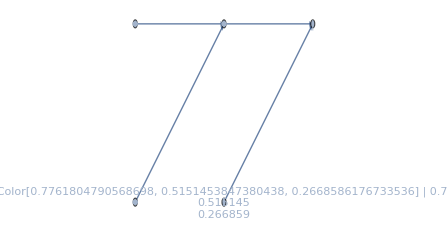

```mathematica
{RandomInteger[1,{2 5+1,2 5+1}],GaussianMatrix[5]}//pipe[
Apply@branchSeq[##&,Times]
,{RandomReal[1,3],##}&
,Apply@branchSeq[##&,Function[{color,mask,ker,kermask},kermask #&/@color]]
,Function[{color,mask,ker,kermask,dist},{
{RGBColor@@color//Magnify[#,2]&,color//Grid[{#}ᵀ,Alignment->"."]&}//Grid[{#},Frame->True]&//Magnify[#,2]&
,{mask,ker,kermask}//Map[pipe[Rescale,Image[#,ImageSize->70]&]]//Apply@Sequence
,{
dist//Rescale//Image[#,ImageSize->70,ColorSpace->"RGB",Interleaving->False]&
,dist//Rescale//Map[Image[#,ImageSize->70]&]//Grid[{#}ᵀ,Alignment->"."]&
}//Grid[{#},Frame->True]&
}]
,Apply@Function[{color,mask,ker,kermask,dist},
{{mask,ker}->kermask,{color,kermask}->dist}//Map[Thread]//Flatten//
Graph[{color,mask,ker,kermask,dist},#
,VertexLabels->Placed["Name",Center]
,EdgeShapeFunction->GraphElementData["CarvedArcArrow","ArrowSize"->0.1]
,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]&
]
]
```

#### Basic Idea

depth of certain pixel P ⟹ λ_P ⟹ PSF for P

image value at P ⟹_(pixels around P)^(randomly (∝ PSF_P) distributed to) image value at pixels around P

## 案例2 / Case 2

#### 单步渲染过程 One rendering step

```mathematica
ClearAll[render]
render[]:=
Module[{offsetMask,weightMask,posMask,multiSampleSet,sampleSet,sampleDepthSet,weightSet,ΔconvLayer}
,$renderPass++
;offsetMask=RandomPoint[$sampleRegion,{$sampleNum,$height,$width}]
;(* A compact support continuous PSF: *)
weightMask=1/(2π ($sampleRadius)^2)psfRadiusFunc[
offsetMask//(#^2).{1,1}&//Transpose[#,{3,1,2}]&//(√#)/($sampleRadius)&
,$psfσMask//Rescale//1-#&
]//Transpose[#,{2,3,1}]&
;weightSet=weightMask//pipe[Transpose[#,{3,1,2}]&,Flatten[#,1]ᵀ&]
;posMask=Reverse[$xyMask]+Transpose[offsetMask,{4,1,2,3}]//Transpose[#,{1,2,4,3}]&
;multiSampleSet=PixelValue[$img,Flatten[posMask,2],Padding->RGBColor[0, 0, 0, 0]]//
ArrayReshape[#,{$width $height,$sampleNum,$imgChl}]ᵀ&
;sampleSet=multiSampleSet weightSet//Total
;ΔconvLayer=sampleSetᵀ//
Map@pipe[
Thread[Flatten[$xyMask,1]->#]&
,SparseArray[#,{$width,$height},0]&
]
;$convLayer=(($renderPass-1)$convLayer+ΔconvLayer)/($renderPass)
;]
```

Gaussian PSF：

```mathematica
Function[{r2,σ},1/(2 π σ)Exp[-r2/(2σ)]]
```

圆盘 PSF：

```mathematica
Function[{r2,λ2},1/(π λ2)UnitStep[λ2-r2]]
```

## 案例2 / Case 2

#### 主渲染循环 Main rendering loop

```mathematica
ClearAll[renderLoop]
renderLoop[n:_Integer:1000]:=While[!$renderStop&&$renderPass<n,render[]]
```

```mathematica
ClearAll[renderLoopContinue]
renderLoopContinue[Δn:_Integer:1000]:=renderLoop[$renderPass+Δn]
```

## 案例2 / Case 2

#### 渲染环境初始化 Renderer initialization

cfg_Association :

"img" | img
"depth" | depthMask
"config" | "sampleNum" | M
"psfσRange" | {σ_min,σ_max}
"psfσTF" | func

```mathematica
ClearAll[renderInit]
renderInit[cfg_Association]:=(
$renderPass=$renderPassDone=0
;$renderStop=True
;$img=cfg["img"]
;$imgChl=Information[$img,"Channels"]
;$depthMask=cfg["depth"]
;{$width,$height}=ImageDimensions@$img
;$sampleNum=cfg["config","sampleNum"]
;$psfσRange=cfg["config","psfσRange"]
;$psfσMask=ImageData[$depthMask,"Real"]//cfg["config","psfσTF"]//Rescale[#,{0,1},$psfσRange]&
;$sampleRadius=$psfσRange⟦2⟧//Echo[#,"$sampleRadius"]&
;$sampleRegion=Disk[{0,0},$sampleRadius]
;$sampleFrac=(Area@$sampleRegion)/($sampleNum)
;$convLayer=ConstantArray[0,{$imgChl,$width,$height}]
;$xyMask=Outer[List,Range[$width],Range[$height]]ᵀ
;)
```

## 案例2 / Case 2

#### 交互渲染 Interactive Rendering

```mathematica
result=Image[Transpose[$sampleFrac $convLayer,{1,3,2}],Interleaving->False,ColorSpace->"RGB"];
```

"« Code »"

S_n:=1/n∑_(i=1)^n A_i
S_(n+1)=1/(n+1)(A_(n+1)+∑_(i=1)^n A_i)=(A_(n+1)+n S_n)/(n+1)

"Screen record"

-Graphics-

## 案例2 / Case 2

#### 最终效果 Final Result

```mathematica
result=Import@"test.png"
```

-Graphics-

-Graphics-		-Graphics-

```mathematica
clearBG=Import@"clearBG.png"
```

-Graphics-

```mathematica
ImageCompose[clearBG,result]
```

-Graphics-

{F=k c+(1-k)bg
F'=k c+(1-k)c'=F-(1-k)bg+(1-k)c'

```mathematica
Module[{f,k,bg=0},
{f,k}=Transpose[$sampleFrac $convLayer,{1,3,2}]//branch[Most,Last]
;Transpose[f,{3,1,2}]-(1-k)bg+(1-k)ImageData[clearBG,"Real"]//
Image[#,Interleaving->True,ColorSpace->"RGB"]&
]
```

-Graphics-

## 案例3：从深度图制作景深效果 —— 快速近似 Case 3: Out-of-focus effect from depth map — the “cheating” mode

问题：同样的效果，如果牺牲一些模型精确度，能否有更快速的实现呢？

Question: What about the same effect, but with more ccomputing efficiency?

## 案例3 / Case 3

### 按深度映射对像素分组 Grouping pixels by their depth

对于8bit色深的深度映射图，我们共有256级灰阶：0≤d≤255

There are 256 levels of shades for depth map using 8bit color depth: 0≤d≤255

```mathematica
DynamicModule[{d=48}
,Column[{
Dynamic[
ImageAdd[img,depthMask//Binarize[#,d/255{1,1}]&//GaussianFilter[#,3]&]//ImageMultiply[#,.75]&//ImageResize[#,Scaled[.5]]&
]
,
Row[{Slider[Dynamic[d],{0,255,1}],Dynamic[d]}]
}]
]
```

-Graphics-

## 案例3 / Case 3

### 对不同深度组使用不同卷积核 Applying different PSF for each depth group

注意透明度通道在卷积时会引入我们不想要的特殊计算规则，因此采用 img//ColorSeparate//ColorCombine 事先转换为一般性的多通道图片是必要的。

Note that img//ColorSeparate//ColorCombine is necessary because alpha channel causes unwanted special treatment.

```mathematica
AbsoluteTiming[
result=Block[{rMax=20,focus=48,img=img//ColorSeparate//ColorCombine},
Function[d,
ImageConvolve[
ImageMultiply[img,depthMask//Binarize[#,d/255{1,1}]&]
,psfKernel[rMax,1-Abs[d-focus]/Max[focus,255-focus]]
,Padding->0]
]/@Range[0,255]//
ImageAdd@@#&//ColorSeparate//ColorCombine[#,"RGB"]&
];
]
```

{19.6974,Null}

```mathematica
result//Information
```

-Graphics-

## 案例3 / Case 3

### 最终效果 Final result

```mathematica
result//branch[Identity,AlphaChannel,RemoveAlphaChannel]//ImageAssemble//ImageResize[#,Scaled[.5]]&
```

-Graphics-

与背景图片合成的效果：
Blending with background image:

-Graphics-

## 案例3 / Case 3

### 我们牺牲了什么？ What is the cost?

深度映射的量化误差带来的画质干扰：

Artifact caused by quantization error of depth map:

-Graphics-		-Graphics-

#### Init

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pipe=RightComposition;
branch=Through@*{##}&;
branchSeq=pipe[branch[##],Apply[Sequence]]&;
```

```mathematica
ClearAll[checkerboard]
checkerboard[width_Integer,height_Integer,step:_Integer:100,gap:{_Integer,_Integer}:{15,5}]:=
ParallelTable[
(UnitStep[Mod[i,step]/step-1/2]+UnitStep[Mod[j,step]/step-1/2])//
Plus[#,(-1)^UnitStep[1-#] 1/3 UnitStep[Mod[i+j,gap⟦1⟧]-gap⟦2⟧]]&
,{i,height},{j,width}]//
Rescale//Image
```